# Gene Networks Demo, X regulates Y

## by Prof. Lee Bardwell, Univ. of California, Irvine

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
pY =Pmax*X^n/(k^n+X^n);
system1 = {
Y'[t] == pY - r*Y[t]
};

initials1 = {Y[0]==Yzero};

fullsystem = Join[system1,initials1];

(* 1. Solve with DSolve *)
DSolve[fullsystem,Y[t],t]
```

{{Y[t]→(ⅇ^(-(t (k^n r+r X^n))/(k^n+X^n)) (-Pmax X^n+ⅇ^((t (k^n r+r X^n))/(k^n+X^n)) Pmax X^n+k^n r Yzero+r X^n Yzero))/(r (k^n+X^n))}}

```mathematica
(* 2. Solve with NDSolve and plot *)
parameters1 = {Pmax->10,X-> 3,k->5,r->1,n->1,Yzero-> 0};solution1 = NDSolve[fullsystem/.parameters1,Y[t],{t,0,20}];
```

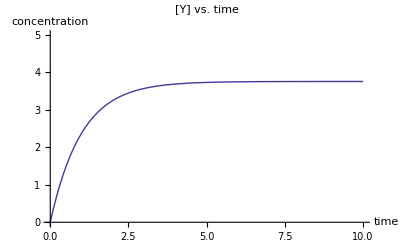

```mathematica
Plot[{Y[t]/.solution1},{t,0,10},PlotStyle->Thick,PlotRange->{0,5},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time"]
```

```mathematica
(* 3. Manipulate the NDSolved solution *)
Manipulate[
parameters1a = {Pmax->PmaxValue,X-> XValue,k->kValue,r->1,n->nValue, Yzero->YzeroValue};
solution2 = NDSolve[fullsystem/.parameters1a,Y[t],{t,0,20}];
Plot[{Y[t]/.solution2,PmaxValue},{t,0,10},PlotStyle->{{Blue,Thick},{Orange,Thick, Dashed}},PlotRange->{0,10},AxesLabel->{"time","[Y]"},PlotLabel->"[Y] vs. time, Y is regulated by X"],
{{PmaxValue,5},1,10,Appearance->"Labeled"},
"Dashed orange line = Pmax",
{{XValue,1},0,10,Appearance->"Labeled"},
{{kValue,1},0.1,10,Appearance->"Labeled"},
{nValue,1,100,Appearance->"Labeled"},
{YzeroValue,0,10,Appearance->"Labeled"}
]
```

-Graphics-

```mathematica
(* 4. Make a manipulatable dose-response curve using "Method #1".   
To use this method we must have an exact steady-state solution. *)
Manipulate[
Plot[Pmax/r*X^n/(k^n+X^n)/.{Pmax->10,r->1} ,{X, 0, Xmax}
,PlotRange ->{0,10.1}, GridLines->{{k},{}},PlotStyle -> {Magenta, Thick},
AxesLabel->{"[X]","Steady-State [Y]"}],
{{k,5},0.1, 50, Appearance-> "Labeled"},
{n,1,100, Appearance-> "Labeled"},
{Xmax,10,200, Appearance-> "Labeled"}

]
```

-Graphics-

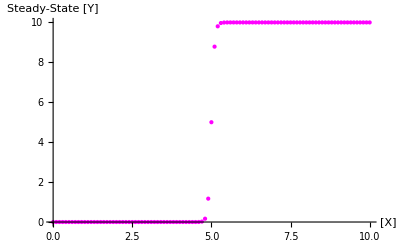

```mathematica
(* 5. Make a dose response curve - Method #2 
(works with any system where we can use NDSolve to estimate steady-state values) *)

parameters1b = {Pmax->10,X-> i,k->5,r->1,n->100,Yzero-> 0};
table1= Table[{i, Y[t] /.Flatten[NDSolve[fullsystem/.parameters1b, {Y[t]}, {t, 0, 20}]] /.t -> 20(*get steady-state value*)}, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange -> All, (*Joined-> True,*)PlotStyle -> {Magenta, Thick},
AxesLabel->{"[X]","Steady-State [Y]"}]
```

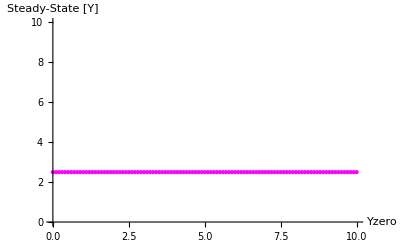

```mathematica
(* 6. Make a dose response curve - This time we will vary the value of Yzero) *)

parameters1c = {Pmax-> 5,X-> 5, k->5,r->1,n->100,Yzero-> i};
table2= Table[{i, Y[t] /.Flatten[NDSolve[fullsystem/.parameters1c, {Y[t]}, {t, 0, 200}]] /.t -> 199(*get steady-state value*)}, {i, 0, 10, 0.1}];
ListPlot[table2, PlotRange -> {0,10}, (*Joined-> True,*)PlotStyle -> {Magenta, Thick},
AxesLabel->{"Yzero","Steady-State [Y]"}]
```

```mathematica
(* 7. Make a manipulatable dose response curve using Method #2.  Note: computationally expensive *)

Manipulate[
parameters1b = {Pmax->10,X-> i,k->5,r->1,n->nValue,Yzero-> 0};
table1= Table[{i, Y[t] /.Flatten[NDSolve[fullsystem/.parameters1b, {Y[t]}, {t, 0, 20}]] /.t -> 20(*get steady-state value*)}, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange -> All, (*Joined-> True,*)PlotStyle -> {Magenta, Thick},
AxesLabel->{"[X]","Steady-State [Y]"}],
{nValue,1,40,1,Appearance->"Labeled"}]
```